Linear Stability Analysis for Bipolar Model

```mathematica
hamil=-omegav Cos[2thetav] PauliMatrix[3]/2+omegav Sin[2thetav]PauliMatrix[1]/2-mu alpha {
{1,epsbar},
{Conjugate@epsbar,-1}}/2
```

{{-(alpha mu)/2-1/2 omegav Cos[2 thetav],-1/2 alpha epsbar mu+1/2 omegav Sin[2 thetav]},{-1/2 alpha mu Conjugate[epsbar]+1/2 omegav Sin[2 thetav],(alpha mu)/2+1/2 omegav Cos[2 thetav]}}

```mathematica
hamilbar=omegav Cos[2thetav] PauliMatrix[3]/2-omegav Sin[2thetav]PauliMatrix[1]/2+mu  {
{1,eps},
{Conjugate@eps,-1}}/2
```

{{mu/2+1/2 omegav Cos[2 thetav],(eps mu)/2-1/2 omegav Sin[2 thetav]},{1/2 mu Conjugate[eps]-1/2 omegav Sin[2 thetav],-mu/2-1/2 omegav Cos[2 thetav]}}

```mathematica
rho=1/2{
{1,eps},
{Conjugate@eps,-1}}
```

{{1/2,eps/2},{Conjugate[eps]/2,-1/2}}

```mathematica
rhobar=1/2{
{1,epsbar},
{Conjugate@epsbar,-1}}
```

{{1/2,epsbar/2},{Conjugate[epsbar]/2,-1/2}}

```mathematica
rhs=hamil.rho-rho.hamil//FullSimplify
rhsbar=hamilbar.rhobar-rhobar.hamilbar//FullSimplify
```

{{1/4 (-alpha epsbar mu Conjugate[eps]+alpha eps mu Conjugate[epsbar]-4 ⅈ omegav Cos[thetav] Im[eps] Sin[thetav]),1/2 (alpha (-eps+epsbar) mu-omegav (eps Cos[2 thetav]+Sin[2 thetav]))},{1/2 (alpha mu (Conjugate[eps]-Conjugate[epsbar])+omegav Conjugate[eps] Cos[2 thetav]+omegav Sin[2 thetav]),1/4 alpha mu (epsbar Conjugate[eps]-eps Conjugate[epsbar])+ⅈ omegav Cos[thetav] Im[eps] Sin[thetav]}}

{{1/4 (-epsbar mu Conjugate[eps]+eps mu Conjugate[epsbar]+4 ⅈ omegav Cos[thetav] Im[epsbar] Sin[thetav]),1/2 ((-eps+epsbar) mu+epsbar omegav Cos[2 thetav]+omegav Sin[2 thetav])},{1/2 (mu Conjugate[eps]-Conjugate[epsbar] (mu+omegav Cos[2 thetav])-omegav Sin[2 thetav]),1/4 (epsbar mu Conjugate[eps]-eps mu Conjugate[epsbar]-4 ⅈ omegav Cos[thetav] Im[epsbar] Sin[thetav])}}

```mathematica
rhs[[1,2]]
rhsbar[[1,2]]
```

1/2 (alpha (-eps+epsbar) mu-omegav (eps Cos[2 thetav]+Sin[2 thetav]))

1/2 ((-eps+epsbar) mu+epsbar omegav Cos[2 thetav]+omegav Sin[2 thetav])

Linearized

```mathematica
epsilon[t]={e[t],ebar[t]}
erhs=1/2{{-alpha mu-omegav,alpha mu},{-mu,mu+omegav}}
```

{e[t],ebar[t]}

{{1/2 (-alpha mu-omegav),(alpha mu)/2},{-mu/2,(mu+omegav)/2}}

```mathematica
I D[epsilon[t],t]==erhs.epsilon[t]
```

{ⅈ e'[t],ⅈ ebar'[t]}=={1/2 (-alpha mu-omegav) e[t]+1/2 alpha mu ebar[t],-1/2 mu e[t]+1/2 (mu+omegav) ebar[t]}

```mathematica
Eigensystem[erhs]//FullSimplify
```

{{1/4 (mu-alpha mu-√((-1+alpha)^2 mu^2+4 (1+alpha) mu omegav+4 omegav^2)),1/4 (mu-alpha mu+√((-1+alpha)^2 mu^2+4 (1+alpha) mu omegav+4 omegav^2))},{{(mu+alpha mu+2 omegav+√((-1+alpha)^2 mu^2+4 (1+alpha) mu omegav+4 omegav^2))/(2 mu),1},{(mu+alpha mu+2 omegav-√((-1+alpha)^2 mu^2+4 (1+alpha) mu omegav+4 omegav^2))/(2 mu),1}}}

```mathematica
Reduce[(-1+alpha)^2 mu^2+4 (1+alpha) mu omegav+4 omegav^2<0,mu]//FullSimplify
```

(alpha==1&&((omegav>0&&2 mu+omegav<0)||(2 mu+omegav>0&&omegav<0)))||(mu+(2 (1+alpha) omegav)/(-1+alpha)^2+(4 √alpha Abs[omegav])/Abs[-1+alpha]^2>0&&mu+(2 (1+alpha) omegav)/(-1+alpha)^2<(4 √alpha Abs[omegav])/Abs[-1+alpha]^2&&omegav≠0)

## Region

```mathematica
mum[alpha_]=2/(1-√alpha)^2
mup[alpha_]=2/(1+√alpha)^2
```

2/(1-√alpha)^2

2/(1+√alpha)^2

```mathematica
Table[
{mum[alpha],mup[alpha]},
{alpha,0,1,0.1}
]
```

{{2.,2.},{4.27767,1.15443},{6.54508,0.954915},{9.77733,0.834918},{14.8051,0.750494},{23.3137,0.686292},{39.3649,0.635083},{74.9627,0.592888},{179.443,0.557281},{759.473,0.526681},{ComplexInfinity,0.5}}

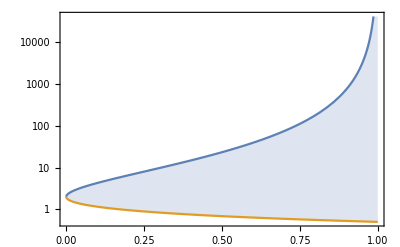

```mathematica
LogPlot[{mum[alpha],mup[alpha]},{alpha,0,1},Frame->True,Filling->{1->{2}}]
```